{{1,0.862168},{2,0.75613},{3,0.673142},{4,0.607086},{5,0.553643},{6,0.509726},{7,0.473108},{8,0.44216},{9,0.41568},{10,0.392767},{11,0.372737},{12,0.355069},{13,0.339355},{14,0.325277},{15,0.31258},{16,0.301063},{17,0.290558},{18,0.280932},{19,0.272072},{20,0.263885},{21,0.256292},{22,0.249233},{23,0.242636},{24,0.236162},{25,0.23446},{26,0.268766},{27,0.0999494},{28,-0.539183},{29,-2.25928},{30,-16.1986},{31,45.8561},{32,-6827.38},{33,3303.08},{34,1.25719×10^6},{35,-1.02244×10^7},{36,1.36386×10^7},{37,2.4582×10^8},{38,2.40977×10^10},{39,-9.983×10^10},{40,-3.29146×10^12}}

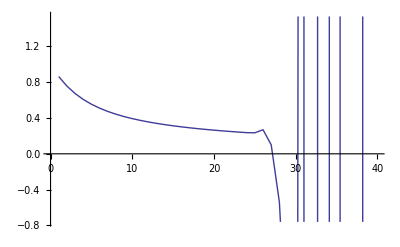

```mathematica
(* The following calculates P[Y|X] *)
pyx = Table[{k,N[∫_0^(2π/3) (1-(θ-Sin[θ])/π)^k*2/3 Sin[θ]ⅆθ]}, {k,1,40}];
Print[pyx];ListLinePlot[pyx]
```

```mathematica
(* The following calculates coverage; see also a.cpp, coverage.R and "Introduction to the Theory of Coverage Processes" page 22 *)
r=1; (* This actually doesn't matter *)

Table[{Simplify[N[(4π r^2- ∫_0^(2π) ∫_r^(2r) x(1-(r^2(2ArcCos[x/(2 r)]-2(√(1-(x/(2r))^2))(x/(2 r))))/(π r^2))^k ⅆxⅆρ)/(π r^2)]]}, {k,1,9}]
(* Simulation results:
  1.420522
1.745786 <-- curiously the formula breaks down for this one
1.980817
2.191605
2.342003
2.458565
2.597797
2.677537
2.728540 *)
```

{{1.4135},{1.0274},{1.98057},{2.17874},{2.33907},{2.47082},{2.58068},{2.67352},{2.75296}}